```mathematica
Maximum-Minimum
```

```mathematica
Manipulate[DynamicModule[{grad,unitgrad,function,buttonText,functionButtons},function[x_,y_]:={5-x^2/2-y^2,x^2/2+y^2,1-2 x+y,x^2/2-y^2,-x^2/2+y^2,Sin[Sin[y]+Sin[x]],x y E^(-0.4 (x^2+y^2))};
buttonText={" maximum"," minimum"," linear"," laddle 1"," saddle 2"," example 1"," example 2"};
functionButtons=Map[#[[1]]->#[[2]]&,Transpose[{Range[Length[buttonText]],buttonText}]];
grad=D[function[x,y][[fff]],{{x,y}}];
unitgrad=grad/Sqrt[grad.grad];
Deploy[GraphicsGrid[{{Plot3D[function[x,y][[fff]],{x,-3,3},{y,-3,3}],Show[{ContourPlot[function[x,y][[fff]],{x,-3,3},{y,-3,3},Contours->10],Graphics[{Red,If[MemberQ[options,gradient],If[MemberQ[options,normalize]&&Dynamic[grad/.{x->pt[[1]],y->pt[[2]]}]=!={0,0},Dynamic[Arrow[{pt,pt+(unitgrad/.{x->pt[[1]],y->pt[[2]]})}]],Dynamic[Tooltip[Arrow[{pt,pt+(grad/.{x->pt[[1]],y->pt[[2]]})}],Style[grad/.{x->pt[[1]],y->pt[[2]]},Red]]],],Red],If[MemberQ[options,normalize],{Black,Dynamic[Circle[pt,1]]},Blue],Blue,If[MemberQ[options,neggradient],If[MemberQ[options,normalize]&&Dynamic[grad/.{x->pt[[1]],y->pt[[2]]}]=!={0,0},Dynamic[Arrow[{pt,pt-(unitgrad/.{x->pt[[1]],y->pt[[2]]})}]],Dynamic[Tooltip[Arrow[{pt,pt-(grad/.{x->pt[[1]],y->pt[[2]]})}],Style[-grad/.{x->pt[[1]],y->pt[[2]]},Blue]]]],Blue],Tooltip[Locator[Dynamic[pt]],Dynamic[pt]]}]},ImageSize->If[MemberQ[options,format],500,380],PlotLabel->If[MemberQ[options,label],ToString[f[x,y],TraditionalForm]<>" = "<>ToString[function[x,y][[fff]],TraditionalForm],Column[{" "},ItemSize->{Automatic,2.75}]]]}}]]],{{options,{gradient},""},{gradient->Style[" ∇f",Red],neggradient->Style[" -∇f",Blue],normalize->" normalize          ",format->Style[" large format",10],label->Style[" show function",10]}},{{fff,1,"function"},functionButtons,ControlType->Setter},{{pt,{1,0},"location"},{-3,-3},{3,3},ImageSize->If[MemberQ[options,format],Medium,Tiny]},ControlType->{CheckboxBar,Setter,Slider2D},ControlPlacement->{Top,Top,Left},Initialization:>{Clear[x,y];
buttonText={" maximum"," minimum"," linear"," saddle 1"," saddle 2"," example 1"," example 2"};
functionButtons=Map[#[[1]]->#[[2]]&,Transpose[{Range[Length[buttonText]],buttonText}]];},AutorunSequencing->{1,2,3}]
```

```mathematica
Gradient Method
```

```mathematica
SynchronousInitialization->False;
Manipulate[DynamicModule[{plt2,plt3,plt4,tbl1,tbl2,tbl3},Dynamic[If[option=="fixed step steepest descent",{uk={p[[1]],p[[2]]};itermax=500;u={u1,u2};alpha=.02;
GradientFixe[fn_,var_List,var0_List,itermax_Integer,ak_]:=Module[{dfn=Grad[fn,var],u=var,uk=var0,pts},pts=Table[uk=uk-ak dfn/.Thread[u->uk],{itermax}];
PrependTo[pts,var0]];
tbl1=GradientFixe[j[u1,u2],u,uk,itermax,alpha];
plt2=ListPlot[{tbl1,tbl1},Joined->{True,False},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,1]}]}];
If[option=="optimal step steepest descent",{uk={p[[1]],p[[2]]};
itermax=500;u={u1,u2};
RL[fon_,var_]:=FindMinimum[fon,{var,0.}][[2,1,2]];
GradientOpt[fn_,var_List,var0_List,itermax_Integer]:=Module[{dfn=Grad[fn,var],v,vark=var0,alpha,h,pts,sk},sk:=Thread[var->vark];
pts=Table[v=vark-alpha dfn/.sk;
h=fn/.Thread[var->v];
vark=v/.alpha->RL[h,alpha],{itermax}];
PrependTo[pts,var0]];
tbl2=Quiet[GradientOpt[j[u1,u2],u,uk,itermax]];
plt3=ListPlot[{tbl2,tbl2},Joined->{True,False},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,1]}]}];
If[option=="conjugate gradient method",{uk={p[[1]],p[[2]]};
itermax=500;u={u1,u2};
GradientConj[fn_,var_List,var0_List,itermax_Integer]:=Module[{dfn=Grad[fn,var],d2fn=Hess[fn,var],dir,vark=var0,ak,betak,oldfn,pts,sk},sk:=Thread[var->vark];
dir=dfn/.sk;
pts=Table[oldfn=N[dfn/.sk];
ak=N[(dir.oldfn)/(dir.d2fn.dir)/.sk];
vark=N[vark-ak dir];
betak=-N[(dfn.dfn)/(oldfn.oldfn)/.sk];
dir=N[(dfn/.sk)-betak dir];
vark,{itermax}];PrependTo[pts,var0]];
tbl3=Quiet[GradientConj[j[u1,u2],u,uk,itermax]];
plt4=ListPlot[{tbl3,tbl3},Joined->{True,False},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,1]}]}];
LocatorPane[Dynamic[p,(p={#[[1]],#[[2]]})&],Dynamic[Which[option=="fixed step steepest descent",Show[plt1,plt2,Graphics[{Red,PointSize[0.025],Point[{1,1}]}],ImageSize->{575,400},ImagePadding->25,PlotRangeClipping->False],option=="optimal step steepest descent",Show[plt1,plt3,Graphics[{Red,PointSize[0.025],Point[{1,1}]}],ImageSize->{575,400},ImagePadding->25,PlotRangeClipping->False],option=="conjugate gradient method",Show[plt1,plt4,Graphics[{Red,PointSize[0.025],Point[{1,1}]}],ImageSize->{575,400},ImagePadding->25,PlotRangeClipping->False]]],{{-1.0,-0.5},{1.0,1.5}}],TrackedSymbols:>{option,p}]],{{p,{-0.5,0.5}},{-1.0,-0.5},{1.0,1.5},None},{{option,"fixed step steepest descent","optimization method"},{"fixed step steepest descent","optimal step steepest descent","conjugate gradient method"}},ControlPlacement->Top,TrackedSymbols:>{option,p},SynchronousUpdating->False,Initialization:>{j[u1_,u2_]:=(u1-1)^2+10 (u1^2-u2)^2;
plt1=ContourPlot[j[u1,u2],{u1,-1,1.5},{u2,-0.5,1.5},Contours->Join[Table[i,{i,0,0.5,0.1}],Table[i,{i,0,20,1}]],ColorFunction->(Blend[{Yellow,Green},2 #]&),ContourLabels->Automatic];
Grad[fon_,var_List]:=D[fon,#]&/@var;
Hess[fon_,var_List]:=Grad[D[fon,#]&/@var,var];}]
```

```mathematica
Newton Method
```

```mathematica
Manipulate[DynamicModule[{sol},sol=Table[Prepend[Quiet@Reap[FindMinimum[f,{vars,start}ᵀ,Method->method,StepMonitor:>Sow[vars]]][[2,1]],start],{method,{"Newton","QuasiNewton","ConjugateGradient"}}];
Show[g,Graphics[{Text[start,{-8,4.05},{-1,1},Background->White],Darker[Green,0.5],Line[sol[[1]]],Point[sol[[1]]],Text["Newton: "<>ToString[Length[sol[[1]]]-1]<>" steps",{0,3.7}],Darker[Blue,0.3],Line[sol[[2]]],Point[sol[[2]]],Text["QuasiNewton: "<>ToString[Length[sol[[2]]]-1]<>" steps",{0,3.2}],Purple,Line[sol[[3]]],Point[sol[[3]]],Text["Conjugate Gradient: "<>ToString[Length[sol[[3]]]-1]<>" steps",{0,2.7}],Red,PointSize[Medium],Point[min]}]]],{{start,{7.15,-13.38}},Locator},SaveDefinitions->True,Initialization:>{f=x^4+3 x^2 y+5 y^2+x+y,vars={x,y},min=vars/.Last[FindMinimum[f,{vars,{0,0}}ᵀ]],g=ContourPlot[f,{x,-8,8},{y,-14,4},Contours->30,ContourShading->False,AspectRatio->Automatic,ImageSize->{460,440},PlotRange->{Full,Full,All},BaseStyle->{FontSize->12},ImagePadding->{{15,1},{18,2}}]}]
```

```mathematica
f[x_,y_,z_]=4x^2+2y^2+z^2−x y+y z−5x−9y+z
```

-5 x+4 x^2-9 y-x y+2 y^2+z+y z+z^2

```mathematica
D[f,{{x,y,z},1}]
```

```mathematica
g [x_,y_]=x^4+y^4-x y
```

x^4-3 x y+y^4

```mathematica
Plot3D[x^4-3 x y+y^4,{x,-20,20},{y,-20,20},Boxed->False,Mesh->None,Axes->True,ColorFunction->Hue]
```

-Graphics3D-

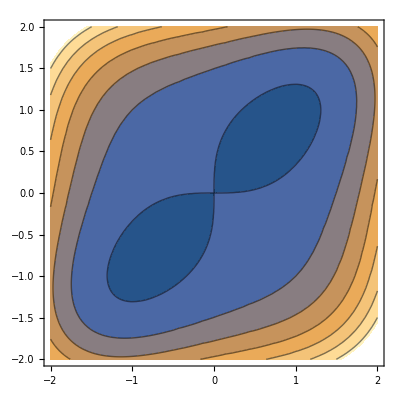

```mathematica
ContourPlot[x^4-3 x y+y^4,{x,-2,2},{y,-2,2}]
```

```mathematica
ff[x_,y_]=1/2(x^2+a  y^2)
```

1/2 (x^2+a y^2)

```mathematica
Manipulate[Plot3D[1/2 (x^2+a y^2),{x,-0.5485147527566367,0.5485147527566367},{y,-0.5485147527566367,0.5485147527566367}, ColorFunction->Hue],{a,-2,10}]
```

Position Triangulation

(-177.956+x21^2+(-10+x22)^2)^2+(-58.0644+(-10+x21)^2+x22^2)^2+(-17.9776+x21^2+x22^2)^2

{0.0000884836,{x21→2.99536,x22→-2.99946}}

-Graphics3D-

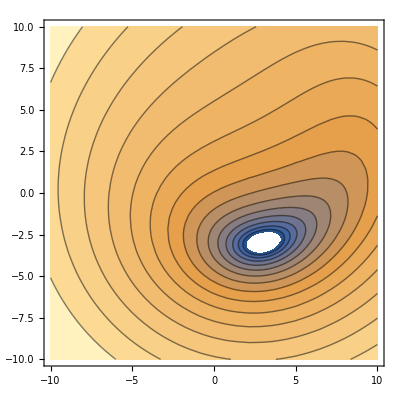

```mathematica
Position Triangulation
dd12=4.24;dd23=7.62;dd24=13.34;
g=((x21)^2+(x22)^2-dd12^2)^2+((x21-10)^2+(x22-0)^2-dd23^2)^2+((x21-0)^2+(x22-10)^2-dd24^2)^2
FindMinimum[g,{x21,x22},Method->"Newton"]
Plot3D[g,{x21,-10,10},{x22,-10,10}]
numC=20;
ContourPlot[Log[g],{x21,-10,10},{x22,-10,10},Contours->15,BaseStyle->{FontSize->25}]
```

```mathematica
Molecular Distance Geometric Problem
```

```mathematica
Solution from R optimx
```

```mathematica
y2={1.4985361,0.2886046,0.003404882}; y3={ 2.080146,-0.06313866, 1.369693};y4={3.550363,0.3433941,1.415593};
```

```mathematica
Graphics3D[{Sphere[x1,.4],Text[1,x1],Sphere[y2,.4],Text[2,y2],Sphere[y3, .4],Text[3,y3],Sphere[y4, .4],Text[4,y4],Cylinder[{x1,y2},1/10],Cylinder[{y3,y2},1/10],Cylinder[{y3,y4},1/10]},Boxed->False]
```

-Graphics3D-